# Ellipse Curve Cryptography 椭圆曲线加密

## ECC--通过椭圆曲线方程式性质产生密钥

保密强度高

计算量小

处理速度快

存储空间&带宽占用量少

## 椭圆曲线示例

y^2==x^3+x+1

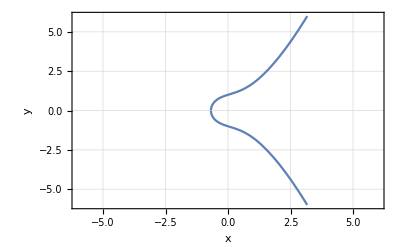

```mathematica
TraditionalForm[y^2==x^3+x+1]
Plot[y1/.Solve[x^3+x+1-y1^2==0],{x,-6,6},PlotRange->{{-6,6},{-6,6}},Frame->True,GridLines->Automatic,FrameLabel->{x,y}]
```

y^2==x^3-x

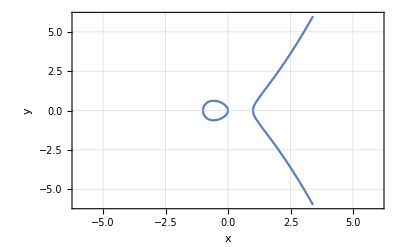

```mathematica
TraditionalForm[y^2==x^3-x]
Plot[y2/.Solve[x^3-x-y2^2==0],{x,-6,6},PlotRange->{{-6,6},{-6,6}},Frame->True,GridLines->Automatic,FrameLabel->{x,y}]
```

```mathematica
TraditionalForm[y^2==x^3-x]
Plot[y2/.Solve[x^3-x-y2^2==0],{x,-6,6},PlotRange->{{-6,6},{-6,6}},Frame->True,GridLines->Automatic,FrameLabel->{x,y}]
```

y^2==x^3-x

-Graphics-

## 非椭圆曲线示例

y^2==x^3+x^2

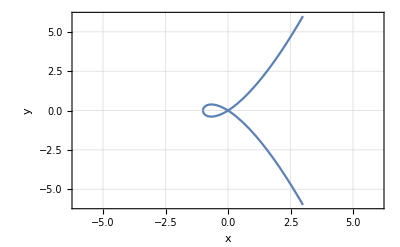

```mathematica
TraditionalForm[y^2==x^3+x^2]
Plot[y3/.Solve[x^3+x^2-y3^2==0],{x,-6,6},PlotRange->{{-6,6},{-6,6}},Frame->True,GridLines->Automatic,FrameLabel->{x,y}]
```

y^2==x^3

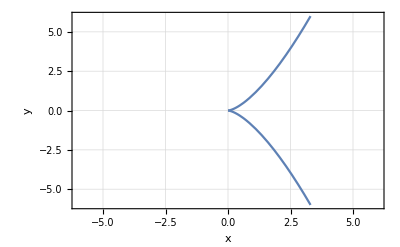

```mathematica
TraditionalForm[y^2==x^3]
Plot[y4/.Solve[x^3-y4^2==0],{x,-6,6},PlotRange->{{-6,6},{-6,6}},Frame->True,GridLines->Automatic,FrameLabel->{x,y}]
```

## 椭圆曲线普通方程

```mathematica
TraditionalForm[y^2+a1 x y+a3 y==x^3+a2 x^2+a4 x+a6]
fx=D[y^2+a1 x y+a3 y==x^3+a2 x^2+a4 x+a6,x]//TraditionalForm
fy=D[y^2+a1 x y+a3 y==x^3+a2 x^2+a4 x+a6,y]//TraditionalForm
```

a1 x y+a3 y+y^2==a2 x^2+a4 x+a6+x^3

a1 y==2 a2 x+a4+3 x^2

a1 x+a3+2 y==0

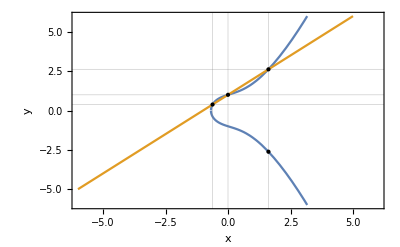

```mathematica
solx=Solve[Sqrt[x^3+x+1]==x+1,x];
p=List[{solx[[1,1,2]],solx[[1,1,2]]+1},{solx[[2,1,2]],solx[[2,1,2]]+1},{solx[[3,1,2]],-solx[[3,1,2]]-1}];

Show[Plot[{y1/.Solve[x^3+x+1-y1^2==0],x+1},{x,-6,6},PlotRange->{{-6,6},{-6,6}},Frame->True,GridLines->{{.5 (1+Sqrt[5]),0,.5 (1-Sqrt[5])},{.5 (1+Sqrt[5])+1,1,.5 (1-Sqrt[5])+1},FrameLabel->{x,y}}],Graphics[{PointSize[Large],Point[p]}],Graphics[Point[{solx[[3,1,2]],solx[[3,1,2]]+1}]],FrameLabel->{x,y}]
```

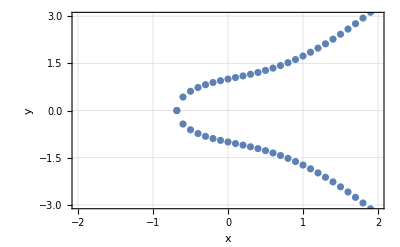

```mathematica
solkzero=Solve[k^3+k+1==0,k][[1,1,2]];
q=List[{solkzero,0}];
Show[ListPlot[Table[{k,y/.Solve[k^3+k+1-y^2==0][[2]]},{k,-2,2,.1}]],ListPlot[Table[{k,y/.Solve[k^3+k+1-y^2==0][[1]]},{k,-2,2,.1}]],ListPlot[q],PlotRange->{{-2,2},{-3,3}},GridLines->Automatic,Frame->True,FrameLabel->{x,y}]
```

```mathematica
Manipulate[ContourPlot[y^2==x^3+a x+b,{x,-5,5},{y,-5,5},Axes->True],{a,-5,5},{b,-5,5}]
```

## 例题

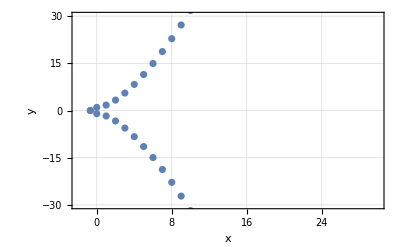

```mathematica
Show[ListPlot[Table[{k,y/.Solve[k^3+k+1-y^2==0][[2]]},{k,-2,30,1}]],ListPlot[Table[{k,y/.Solve[k^3+k+1-y^2==0][[1]]},{k,-2,30,1}]],ListPlot[q],PlotRange->{{-2,30},{-30,30}},GridLines->Automatic,Frame->True,FrameLabel->{x,y}]
```

## E23(1,1)

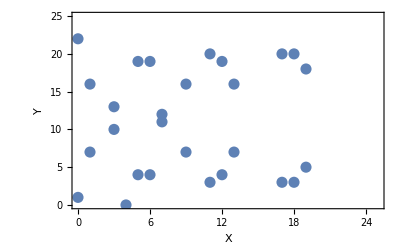

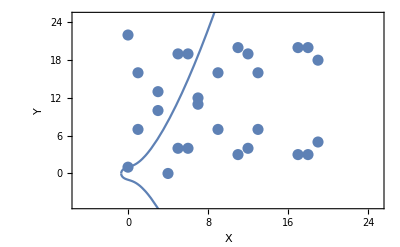

```mathematica
a=1;b=1;
q=23;pts={};
For[x=0,x<q,x++,
For[y=0,y<q,y++,
If[Mod[y^2-x^3-a x-b,q]==0,pts=Append[pts,{x,y}]]]];
pts//StandardForm;
Ecc=ListPlot[pts,PlotStyle->PointSize[0.02],PlotRange->{{0,25},{0,25}},Frame->True,FrameLabel->{X,Y}]
Show[Ecc,Plot[{y1/.Solve[x^3+x+1-y1^2==0]},{x,-5,25}],PlotRange->{{-5,25},{-5,25}}]
```

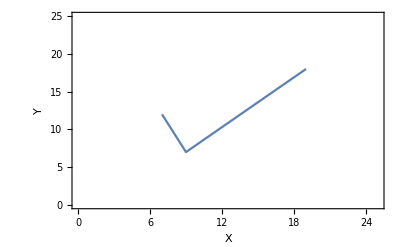

```mathematica
P={7,12};Q={9,7};
ka=Mod[(Q[[2]]-P[[2]])*PowerMod[Q[[1]]-P[[1]],-1,q],q];
x3=Mod[ka^2-P[[1]]-Q[[1]],q];
y3=Mod[-ka(x3-P[[1]])-P[[2]],q];
R={x3,y3};
addition={P,Q,R};
ListPlot[addition,Joined->True,PlotRange->{{0,25},{0,25}},PlotStyle->PointSize[0.02],Frame->True,FrameLabel->{X,Y}]
```

{12,4}

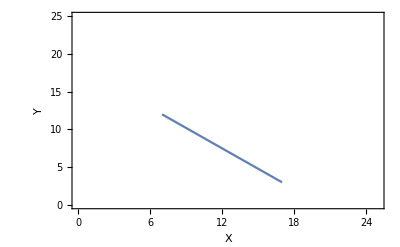

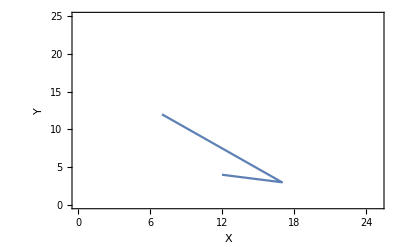

```mathematica
ki=Mod[(3*P[[1]]^2+a)*PowerMod[2 P[[2]],-1,q],q];
x4=Mod[ki^2-2 P[[1]],q];
y4=Mod[-ki (x4-P[[1]])-P[[2]],q];
S={x4,y4};
list4={P,S};
k5=Mod[(S[[2]]-P[[2]])*PowerMod[S[[1]]-P[[1]],-1,q],q];
x5=Mod[k5^2-P[[1]]-S[[1]],q];
y5=Mod[-k5(x5-P[[1]])-P[[2]],q];
T={x5,y5}
list5={P,S,T};
ListPlot[list4,Joined->True,PlotRange->{{0,25},{0,25}},PlotStyle->PointSize[0.02],Frame->True,FrameLabel->{X,Y}]
ListPlot[list5,Joined->True,PlotRange->{{0,25},{0,25}},PlotStyle->PointSize[0.02],Frame->True,FrameLabel->{X,Y}]
```

```mathematica
U[0]=S;
Do[k1=Mod[(U[n][[2]]-P[[2]])*PowerMod[U[n][[1]]-P[[1]],-1,q],q];
x1=Mod[k1^2-P[[1]]-U[n][[1]],q];
y1=Mod[-k1(x1-P[[1]])-P[[2]],q];
U[n+1]={x1,y1};,{n,0,30}]
```

PowerMod::ninv: 0 is not invertible modulo 23.

```mathematica
Print[U[5]];
E23list=Table[U[n],{n,0,25}]
ListPlot[{list4,E23list},Joined->True,PlotRange->{{0,25},{0,25}},PlotStyle->PointSize[0.02],Frame->True,FrameLabel->{X,Y},GridLines->Automatic]
```

{4,0}

## E29(4,20)空间

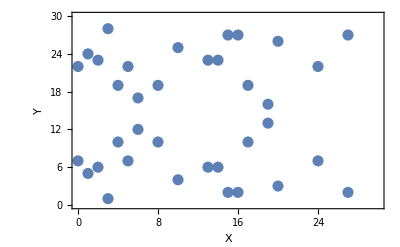

```mathematica
a=4;b=20;q=29;pts={};
For[x=0,x<q,x++,
For[y=0,y<q,y++,
If[Mod[y^2-x^3-a x-b,q]==0,pts=Append[pts,{x,y}]]]];
pts//StandardForm;
Ecc=ListPlot[pts,PlotStyle->PointSize[0.02],PlotRange->{{0,30},{0,30}},Frame->True,FrameLabel->{X,Y}]
```

### 由初始态开始到2P点的计算（2）

#### 初始点为G（13，23）

```mathematica
initP={13,23};
k6=Mod[(3*initP[[1]]^2+a)*PowerMod[2 initP[[2]],-1,q],q];
x6=Mod[k6^2-2 initP[[1]],q];
y6=Mod[-k6 (x6-initP[[1]])-initP[[2]],q];
U[0]={x6,y6}
list6={initP,U[0]};
```

{27,27}

### 从3P点开始的计算（计算结果为k-2，k为私钥）

PowerMod::ninv: 0 is not invertible modulo 29.

{14,6}

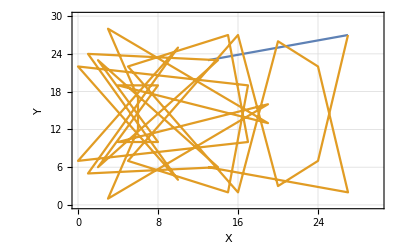

```mathematica
Do[k1=Mod[(U[n][[2]]-initP[[2]])*PowerMod[U[n][[1]]-initP[[1]],-1,q],q];
x1=Mod[k1^2-initP[[1]]-U[n][[1]],q];
y1=Mod[-k1(x1-initP[[1]])-initP[[2]],q];
U[n+1]={x1,y1};,{n,0,37}]
Print[U[23]];
E29list=Table[U[n],{n,0,34}]; (*the order of E29(4,20) is 34 + 2 + 1 = 37*)
ListPlot[{list6,E29list},Joined->True,PlotRange->{{0,30},{0,30}},PlotStyle->PointSize[0.02],Frame->True,FrameLabel->{X,Y},GridLines->Automatic]
```

#### 加密内容为M（3，28），私钥k为25，K为公钥的情况

```mathematica
M={3,28};
K=U[23];(*n=k-3, (14,6)*)
(*E29(4,20) nP space*)
cx=Mod[6 25 ,37];(*In E29(4,20) nP space, 6*25 G = Mod(150, 37) = 2*G *)
(*M + 2G calculation space *)
k7=Mod[(U[cx-2][[2]]-M[[2]])*PowerMod[U[cx-2][[1]]-M[[1]],-1,q],q];
x7=Mod[k7^2-M[[1]]-U[cx-2][[1]],q];
y7=Mod[-k7(x7-M[[1]])-M[[2]],q];
c1={x7,y7};(*(6,12)*)
c2=U[4];(*6 initP, n=6-2, (5,7)*)
mc2=Mod[{U[cx-2][[1]],-U[cx-2][[2]]},q];(*calculations of (-P) in E29(4,20) space, (27,2)*)
(*c1-c2 calculation space, c1 + mc2 in E29(4,20) space*)
k8=Mod[(mc2[[2]]-c1[[2]])*PowerMod[mc2[[1]]-c1[[1]],-1,q],q];
x8=Mod[k8^2-c1[[1]]-mc2[[1]],q];
y8=Mod[-k8(x8-c1[[1]])-c1[[2]],q];
m={x8,y8}
```

{3,28}